```mathematica
Quit[]
```

```mathematica
NotebookDirectory[]
```

/home/riccardo/Documents/Fisica/Tesi/maindir/pmm2L_noplanar_massless_notr/ifdefinition/

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m";
<<"/home/riccardo/Programs/FormCalc/FormCalc-9.10/FormCalc.m";
Remove[q1];
Remove[q2];
<<"/home/riccardo/Programs/ABISS/ABISS/ABISS.m";
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

```mathematica
SetPath[NotebookDirectory[]];
process={F[3,{1,o}],-F[3,{1,o}]}->{F[2,{2}],-F[2,{2}]};
SetProcess[process];
```

```mathematica
GenerateInput[];
```

ABISS Warning: Input file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm2L_noplanar_massless_notr/ifdefinition/input/kinematics.m already exist. It will NOT be overwritten.

ABISS Warning: Input file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm2L_noplanar_massless_notr/ifdefinition/input/integral_families.m already exist. It will NOT be overwritten.

```mathematica
ImportInput[];
```

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm2L_noplanar_massless_notr/ifdefinition/input/kinematics.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm2L_noplanar_massless_notr/ifdefinition/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm2L_noplanar_massless_notr/ifdefinition/input/equivalence_classes.m

## Diagram Backup

## Load

```mathematica
fieldsBorn=<<(NotebookDirectory[]<>"../backup/fields/fieldsBorn.m");
fields1L=<<(NotebookDirectory[]<>"../backup/fields/fields1L.m");
fields2Lnoplanar=<<(NotebookDirectory[]<>"../backup/fields/fields2L.m");
```

## Prop lists

## Paint

> Top. 1 aebe/cfdg/ehfg1f21212hgh.m, 0 diagrams

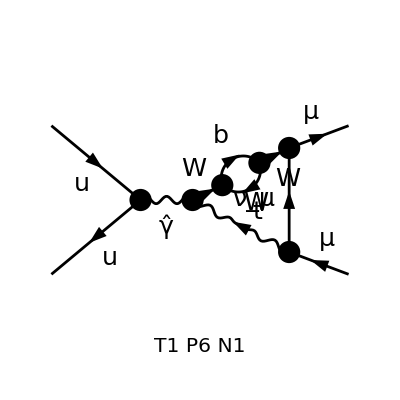

```mathematica
Paint[DiagramExtract[fields2L,1000],ColumnsXRows->1];
```

```mathematica
Paint[fields2Lnoplanar];
```

## Amplitude Backup

```mathematica
myAmpBorn=<<(NotebookDirectory[]<>"../feynArts_amplitudes/BornAmplitudes.m");<
myAmp1L=<<(NotebookDirectory[]<>"../feynArts_amplitudes/OneLoopAmplitudes.m");
myAmp2L=<<(NotebookDirectory[]<>"../feynArts_amplitudes/TwoLoopAmplitudes.m");
Print["Number of diagrams: ", {myAmpBorn,myAmp1L,myAmp2L}//Map[Length]]
```

Set::write: Tag \!\(\*RowBox[{"Less"}]\) in \!\(\*RowBox[{"Null", "<", "myAmp1L"}]\) is Protected.

Number of diagrams: {1,0,1028}

Modellistica
analisi
aziende che cercano rpfili qualificati
avere un dottorato vuol dire dimostrare di essere in grado di sviluppare un pensiero scientifico e originale

## Interference

### Mass Options

```mathematica
normalMass={};
SetZeroMassParticles[normalMass]
```

```mathematica
zeroMass={mu->0,md->0,ms->0,me->0,mm->0};
SetZeroMassParticles[zeroMass]
```

```mathematica
(*myAmpBorn=myAmpBorn/.zeroOnShellMass;
myAmp1L=myAmp1L/.zeroOnShellMass;*)
```

### Computation

```mathematica
ImportInput[]
```

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm2L_noplanar_massless_notr/ifdefinition/input/kinematics.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm2L_noplanar_massless_notr/ifdefinition/input/integral_families.m.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm2L_noplanar_massless_notr/ifdefinition/input/equivalence_classes.m

We want an estimate of the computational time

```mathematica
testFactor=FermionChain[NonCommutative[DiracSpinor[-FourMomentum[Incoming, 2], MU]], EL*NonCommutative[ChiralityProjector[1]]+EL*NonCommutative[ChiralityProjector[-1]],NonCommutative[DiracSpinor[FourMomentum[Incoming, 1], MU]]]*
 FermionChain[NonCommutative[DiracSpinor[FourMomentum[Outgoing, 1], MM]], EL*NonCommutative[ChiralityProjector[1]]+EL*NonCommutative[ChiralityProjector[-1]],NonCommutative[DiracSpinor[-FourMomentum[Outgoing, 2], MM]]]*PropagatorDenominator[FourMomentum[Outgoing,1]+FourMomentum[Outgoing,2],0]/EL^2
```

1/EL^2 DiracSpinor[-(p2),MU].(EL ChiralityProjector[-1]+EL ChiralityProjector[1]).DiracSpinor[p1,MU] DiracSpinor[k1,MM].(EL ChiralityProjector[-1]+EL ChiralityProjector[1]).DiracSpinor[-(k2),MM] 1/(k1+k2)^2

```mathematica
Length[myAmp2L]
```

750

#### Test calculations

```mathematica
Do[
Print[i, "  ",Length[Cases[myAmp2L[[i]],FeynAmpDenominator[___],Infinity]]]
,{i,Length[myAmp2L]}]
```

1  1

2  1

3  1

4  1

5  1

6  1

7  1

8  1

9  1

10  1

11  1

12  1

13  1

14  1

15  1

16  1

17  1

18  1

19  1

20  1

21  1

22  1

23  1

24  1

25  1

26  1

27  1

28  1

29  1

30  1

31  1

32  1

33  1

34  1

35  1

36  1

37  1

38  1

39  1

40  1

41  1

42  1

43  1

44  1

45  1

46  1

47  1

48  1

49  1

50  1

51  1

52  1

53  1

54  1

55  1

56  1

57  1

58  1

59  1

60  1

61  1

62  1

63  1

64  1

65  1

66  1

67  1

68  1

69  1

70  1

71  1

72  1

73  1

74  1

75  1

76  1

77  1

78  1

79  1

80  1

81  1

82  1

83  1

84  1

85  1

86  1

87  1

88  1

89  1

90  1

91  1

92  1

93  1

94  1

95  1

96  1

97  1

98  1

99  1

100  1

101  1

102  1

103  1

104  1

105  1

106  1

107  1

108  1

109  1

110  1

111  1

112  1

113  1

114  1

115  1

116  1

117  1

118  1

119  1

120  1

121  1

122  1

123  1

124  1

125  1

126  1

127  1

128  1

129  1

130  1

131  1

132  1

133  1

134  1

135  1

136  1

137  1

138  1

139  1

140  1

141  1

142  1

143  1

144  1

145  1

146  1

147  1

148  1

149  2

150  2

151  2

152  2

153  2

154  2

155  2

156  2

157  2

158  2

159  2

160  2

161  2

162  2

163  2

164  2

165  2

166  2

167  2

168  2

169  2

170  2

171  2

172  2

173  2

174  2

175  2

176  2

177  2

178  2

179  2

180  2

181  2

182  2

183  2

184  2

185  2

186  2

187  2

188  2

189  2

190  2

191  2

192  2

193  2

194  2

195  2

196  2

197  2

198  2

199  2

200  2

201  2

202  2

203  2

204  2

205  2

206  2

207  2

208  2

209  1

210  1

211  1

212  1

213  1

214  1

215  1

216  1

217  1

218  1

219  1

220  1

221  1

222  1

223  1

224  1

225  1

226  1

227  1

228  1

229  1

230  1

231  1

232  1

233  1

234  1

235  1

236  1

237  1

238  1

239  1

240  1

241  1

242  1

243  1

244  1

245  1

246  1

247  1

248  1

249  1

250  1

251  1

252  1

253  1

254  1

255  1

256  1

257  1

258  1

259  1

260  1

261  1

262  1

263  1

264  1

265  1

266  1

267  1

268  1

269  1

270  1

271  1

272  1

273  1

274  1

275  1

276  1

277  1

278  1

279  1

280  1

281  1

282  1

283  1

284  1

285  1

286  1

287  1

288  1

289  1

290  1

291  1

292  1

293  1

294  1

295  1

296  1

297  1

298  1

299  1

300  1

301  1

302  1

303  1

304  1

305  1

306  1

307  1

308  1

309  1

310  1

311  1

312  1

313  1

314  1

315  1

316  1

317  1

318  1

319  1

320  1

321  1

322  1

323  1

324  1

325  1

326  1

327  1

328  1

329  1

330  1

331  1

332  1

333  1

334  1

335  1

336  1

337  1

338  1

339  1

340  1

341  1

342  1

343  1

344  1

345  1

346  1

347  1

348  1

349  1

350  1

351  1

352  1

353  1

354  1

355  1

356  1

357  1

358  1

359  1

360  1

361  1

362  1

363  1

364  1

365  1

366  1

367  1

368  1

369  1

370  1

371  1

372  1

373  1

374  1

375  1

376  1

377  1

378  1

379  1

380  1

381  1

382  1

383  1

384  1

385  1

386  1

387  1

388  1

389  1

390  1

391  1

392  1

393  1

394  1

395  1

396  1

397  1

398  1

399  1

400  1

401  1

402  1

403  1

404  1

405  1

406  1

407  1

408  1

409  1

410  1

411  1

412  1

413  1

414  1

415  1

416  1

417  1

418  1

419  1

420  1

421  1

422  1

423  1

424  1

425  1

426  1

427  1

428  1

429  1

430  1

431  1

432  1

433  1

434  1

435  1

436  1

437  1

438  1

439  1

440  1

441  1

442  1

443  1

444  1

445  1

446  1

447  1

448  1

449  1

450  1

451  1

452  1

453  1

454  1

455  1

456  1

457  1

458  1

459  1

460  1

461  1

462  1

463  1

464  1

465  1

466  1

467  1

468  1

469  1

470  1

471  1

472  1

473  1

474  1

475  1

476  1

477  1

478  1

479  1

480  1

481  1

482  1

483  1

484  1

485  1

486  1

487  1

488  1

489  1

490  1

491  1

492  1

493  1

494  1

495  1

496  1

497  1

498  1

499  1

500  1

501  1

502  1

503  1

504  1

505  1

506  1

507  1

508  1

509  1

510  1

511  1

512  1

513  1

514  1

515  1

516  1

517  1

518  1

519  1

520  1

521  1

522  1

523  1

524  1

525  1

526  1

527  1

528  1

529  1

530  1

531  1

532  1

533  1

534  1

535  1

536  1

537  1

538  1

539  1

540  1

541  1

542  1

543  1

544  1

545  1

546  1

547  1

548  1

549  1

550  1

551  1

552  1

553  1

554  1

555  1

556  1

557  1

558  1

559  1

560  1

561  1

562  1

563  1

564  1

565  1

566  1

567  1

568  1

569  1

570  1

571  1

572  1

573  1

574  1

575  1

576  1

577  1

578  1

579  1

580  1

581  1

582  1

583  1

584  1

585  1

586  1

587  1

588  1

589  1

590  1

591  1

592  1

593  1

594  1

595  1

596  1

597  1

598  1

599  1

600  1

601  1

602  1

603  1

604  1

605  1

606  1

607  1

608  1

609  1

610  1

611  1

612  1

613  1

614  1

615  1

616  1

617  1

618  1

619  1

620  1

621  1

622  1

623  1

624  1

625  1

626  1

627  1

628  1

629  1

630  1

631  1

632  1

633  1

634  1

635  1

636  1

637  1

638  1

639  1

640  1

641  1

642  1

643  1

644  1

645  1

646  1

647  1

648  1

649  1

650  1

651  1

652  1

653  1

654  1

655  1

656  1

657  1

658  1

659  1

660  1

661  1

662  1

663  1

664  1

665  1

666  1

667  1

668  1

669  1

670  1

671  1

672  1

673  1

674  1

675  1

676  1

677  1

678  1

679  1

680  1

681  1

682  1

683  1

684  1

685  1

686  1

687  1

688  1

689  1

690  1

691  1

692  1

693  1

694  1

695  1

696  1

697  1

698  1

699  1

700  1

701  1

702  1

703  1

704  1

705  1

706  1

707  1

708  1

709  1

710  1

711  1

712  1

713  1

714  1

715  1

716  1

717  1

718  1

719  1

720  1

721  1

722  1

723  1

724  1

725  1

726  1

727  1

728  1

729  1

730  1

731  1

732  1

733  1

734  1

735  1

736  1

737  1

738  1

739  1

740  1

741  1

742  1

743  1

744  1

745  1

746  1

747  1

748  1

749  1

750  1

```mathematica
myAmp2L[[207]]
```

-ⅈ (2 π)^(-2 d) μ^(2 (4-d)) v̄[p2,MU].(ⅈ EL gAu ga[Lor1].om_-+ⅈ EL gAu ga[Lor1].om_+).u[p1,MU] ū[k1,MM].(ⅈ EL gZlL ga[Lor3].om_-+ⅈ EL gZlR ga[Lor3].om_+).(MM+gs[-(q1)]).(ⅈ EL gAl ga[Lor2].om_-+ⅈ EL gAl ga[Lor2].om_+).(MM+gs[-(q1)-k1-k2]).(ⅈ EL gAl ga[Lor5].om_-+ⅈ EL gAl ga[Lor5].om_+).v[k2,MM] FeynAmpDenominator[1/(-MW^2+(q2)^2)] FeynAmpDenominator[1/(-MM^2+(q1)^2),1/(q1+k1)^2,1/(-MZ^2+(q1+k1)^2),1/(-MM^2+(q1+k1+k2)^2)] g[Lor1,Lor2] g[Lor3,Lor4] g[Lor5,Lor6] g[Lor7,Lor8] (-ⅈ EL^2 gWWAZ g[Lor4,Lor8] g[Lor6,Lor7]-ⅈ EL^2 gWWAZ g[Lor4,Lor7] g[Lor6,Lor8]+2 ⅈ EL^2 gWWAZ g[Lor4,Lor6] g[Lor7,Lor8]) 1/(k1+k2)^2

```mathematica
myAmpBorn[[1]]
```

v̄[p2,MU].(ⅈ EL gAu ga[Lor1].om_-+ⅈ EL gAu ga[Lor1].om_+).u[p1,MU] ū[k1,MM].(ⅈ EL gAl ga[Lor2].om_-+ⅈ EL gAl ga[Lor2].om_+).v[k2,MM] g[Lor1,Lor2] 1/(k1+k2)^2

```mathematica
AmpSquare[myAmp2L[[207]],myAmpBorn[[1]]]//Simplify
```

1/(mz^2 s^2)4^-d (-1+d) EL^8 gAl^3 gAu^2 gWWAZ (gZlL+gZlR) π^(-2 d) μ^(8-2 d) (PropList[KiraPropagator[q1,0],KiraPropagator[p1+p2+q1,0],KiraPropagator[p3+q1,0],KiraPropagator[q2,mw]]-PropList[KiraPropagator[q1,0],KiraPropagator[p1+p2+q1,0],KiraPropagator[p3+q1,mz],KiraPropagator[q2,mw]]) (((-20+6 d) s^2+2 (-10+3 d) s t+4 (-2+d) t^2) SPList[SP[p1,q1]]+2 (2 (-2+d) s^2+(2+d) s t+2 (-2+d) t^2) SPList[SP[p2,q1]]+36 s^2 SPList[SP[p3,q1]]-18 d s^2 SPList[SP[p3,q1]]+2 d^2 s^2 SPList[SP[p3,q1]]+8 s^2 SPList[SP[q1,q1]]-6 d s^2 SPList[SP[q1,q1]]+d^2 s^2 SPList[SP[q1,q1]]-8 s t SPList[SP[q1,q1]]+4 d s t SPList[SP[q1,q1]]-8 t^2 SPList[SP[q1,q1]]+4 d t^2 SPList[SP[q1,q1]]+8 s SPList[SP[p1,q1],SP[p1,q1]]-4 d s SPList[SP[p1,q1],SP[p1,q1]]+8 t SPList[SP[p1,q1],SP[p1,q1]]-4 d t SPList[SP[p1,q1],SP[p1,q1]]-8 s SPList[SP[p1,q1],SP[p2,q1]]+4 d s SPList[SP[p1,q1],SP[p2,q1]]-24 s SPList[SP[p1,q1],SP[p3,q1]]+12 d s SPList[SP[p1,q1],SP[p3,q1]]-16 t SPList[SP[p1,q1],SP[p3,q1]]+8 d t SPList[SP[p1,q1],SP[p3,q1]]-8 t SPList[SP[p2,q1],SP[p2,q1]]+4 d t SPList[SP[p2,q1],SP[p2,q1]]-8 s SPList[SP[p2,q1],SP[p3,q1]]+4 d s SPList[SP[p2,q1],SP[p3,q1]]+16 t SPList[SP[p2,q1],SP[p3,q1]]-8 d t SPList[SP[p2,q1],SP[p3,q1]]+16 s SPList[SP[p3,q1],SP[p3,q1]]-8 d s SPList[SP[p3,q1],SP[p3,q1]])

```mathematica
pl= Cases[sm[[207]],PropList[___],Infinity];
plc=Map[Coefficient[sm[[207]],#]&,pl];
(plc[[1]]-plc[[2]])//Simplify
(plc[[1]]+plc[[2]])//Simplify
```

1/(mz^2 s^2)2^(1-2 d) EL^8 gAl^3 gAu^2 gWWAZ (gZlL+gZlR) π^(-2 d) μ^(8-2 d) (-2 (1-d) ((-10+3 d) s^2+(-10+3 d) s t+2 (-2+d) t^2) SPList[SP[p1,q1]]-2 (1-d) (2 (-2+d) s^2+(2+d) s t+2 (-2+d) t^2) SPList[SP[p2,q1]]+2 (-18+27 d-10 d^2+d^3) s^2 SPList[SP[p3,q1]]+(2-3 d+d^2) ((-4+d) s^2+4 s t+4 t^2) SPList[SP[q1,q1]]-4 (2-3 d+d^2) (s+t) SPList[SP[p1,q1],SP[p1,q1]]+4 (2-3 d+d^2) s SPList[SP[p1,q1],SP[p2,q1]]+4 (2-3 d+d^2) (3 s+2 t) SPList[SP[p1,q1],SP[p3,q1]]+4 (2-3 d+d^2) t SPList[SP[p2,q1],SP[p2,q1]]+4 (2-3 d+d^2) (s-2 t) SPList[SP[p2,q1],SP[p3,q1]]-8 (2-3 d+d^2) s SPList[SP[p3,q1],SP[p3,q1]])

0

```mathematica
Do[
Print[Length[Cases[sm[[i]],PropList[___],Infinity]]]
,{i,149,208}]
```

0

0

0

«3 more identical outputs»

1

1

1

«3 more identical outputs»

0

0

0

«3 more identical outputs»

1

1

1

«3 more identical outputs»

0

0

0

«3 more identical outputs»

1

1

1

«7 more identical outputs»

0

0

0

«7 more identical outputs»

1

2

2

1

1

1

«1 more identical outputs»

2

2

1

> Top. 1 aebe/cfdg/ehfhfighgiii.m, 0 diagrams

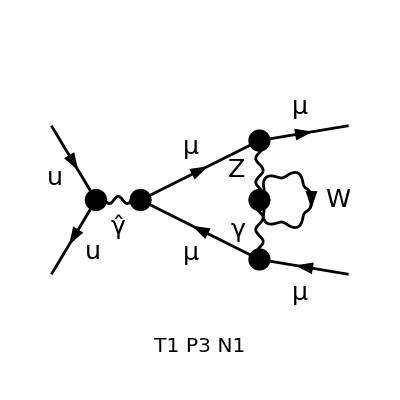

```mathematica
Paint[DiagramExtract[fields2Lnoplanar,207],ColumnsXRows->1];
```

```mathematica
AmpSquare[myAmp2L[[149]],testFactor]
```

0

```mathematica
Do[
Print[sm[[i]]]
,{i,149,208}]
```

#### End of Test

```mathematica
faDenominators={};
Do[
faden=Cases[myAmp2L[[i]],FeynAmpDenominator[x___]:>x,Infinity];
faden=FeynAmpDenominator@@faden;
faDenominators=Append[faDenominators,faden]
,{i,Length[myAmp2L]}]
Length[faDenominators]
```

1028

```mathematica
Length[faDenominators]
```

1028

```mathematica
plDenominators=Map[AmpSquare[#*testFactor,testFactor]&,faDenominators];
Length[plDenominators]
```

1028

```mathematica
testFactorN=FermionChain[NonCommutative[DiracSpinor[-FourMomentum[Incoming, 2], MU]], EL*NonCommutative[DiracSlash[n]],NonCommutative[DiracSpinor[FourMomentum[Incoming, 1], MU]]]*
 FermionChain[NonCommutative[DiracSpinor[FourMomentum[Outgoing, 1], MM]],EL*NonCommutative[DiracSlash[n]],NonCommutative[DiracSpinor[-FourMomentum[Outgoing, 2], MM]]]*PropagatorDenominator[FourMomentum[Outgoing,1]+FourMomentum[Outgoing,2],0]/EL^2
```

(DiracSpinor[-(p2),MU].(EL DiracSlash[n]).DiracSpinor[p1,MU] DiracSpinor[k1,MM].(EL DiracSlash[n]).DiracSpinor[-(k2),MM] 1/(k1+k2)^2)/EL^2

```mathematica
AmpSquare[testFactorN,testFactor]
```

0

```mathematica
sm=Table[<<(NotebookDirectory[]<>"../interferences/Contribution_"<>ToString[i]<>"_1.m"),{i,1028}];
```

```mathematica
sm[[676]]
```

PropList[KiraPropagator[q1,0],KiraPropagator[p3+q1,mw],KiraPropagator[p3+q1,mw],KiraPropagator[-p1-p2+p3+q1,mw],KiraPropagator[p3+q1-q2,mt],KiraPropagator[q2,mb]] ((3 4^-d (-2+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((-2+d) s^2+4 s t+4 t^2) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p3,q1]])/s+(3 4^-d (-2+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((-2+d) s^2+4 s t+4 t^2) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[q1,q1]])/s-(3 4^-d (-2+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((-2+d) s^2+4 s t+4 t^2) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[q1,q2]])/s-(3 2^(1-2 d) d EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((-4+d) s-2 t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,p3],SP[p3,q1]])/s-1/s^2 3 2^(1-2 d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) (3 (-4+d) s^2+(-56+25 d-3 d^2) s t-2 (20-9 d+d^2) t^2) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,p3],SP[q1,q1]]+(3 4^(1-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((-4+d) s-2 t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,p3],SP[q1,q2]])/s-1/s^2 3 2^(1-2 d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((36-20 d+3 d^2) s^2+2 (44-22 d+3 d^2) s t+4 (14-7 d+d^2) t^2) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p3,q1]]+1/s^2 3 2^(1-2 d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) (2 (18-8 d+d^2) s^2+(48-20 d+3 d^2) s t+2 (12-6 d+d^2) t^2) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p3,q2]]-1/s^2 3 2^(1-2 d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) (4 (-4+d) s^2+(-68+28 d-3 d^2) s t-2 (24-10 d+d^2) t^2) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[q1,q2]]+1/s^2 3 2^(1-2 d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) (3 (-4+d) s^2+(-16+3 d) s t+2 (-4+d) t^2) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[q2,q2]]+(3 2^(1-2 d) d EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((-4+d) s-2 t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q2],SP[p3,q1]])/s+1/s^2 3 2^(1-2 d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) (3 (-4+d) s^2+(-56+25 d-3 d^2) s t-2 (20-9 d+d^2) t^2) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q2],SP[q1,q1]]-(3 4^(1-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((-4+d) s-2 t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q2],SP[q1,q2]])/s-(3 2^(1-2 d) d EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((-2+d) s+2 t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,p3],SP[p3,q1]])/s-1/s^2 3 2^(1-2 d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((-2+d)^2 s^2-(24-11 d+d^2) s t-2 (20-9 d+d^2) t^2) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,p3],SP[q1,q1]]+(3 4^(1-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((-2+d) s+2 t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,p3],SP[q1,q2]])/s-1/s^2 3 2^(1-2 d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((-2+d)^2 s^2+2 (12-6 d+d^2) s t+4 (14-7 d+d^2) t^2) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,q1],SP[p3,q1]]+1/s^2 3 2^(1-2 d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((12-8 d+d^2) s^2+(-4+d) d s t+2 (12-6 d+d^2) t^2) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,q1],SP[p3,q2]]-1/s^2 3 2^(1-2 d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((-2+d)^2 s^2-(28-12 d+d^2) s t-2 (24-10 d+d^2) t^2) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,q1],SP[q1,q2]]+1/s^2 3 2^(1-2 d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) (2 (-2+d) s^2+d s t+2 (-4+d) t^2) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,q1],SP[q2,q2]]+(3 2^(1-2 d) d EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((-2+d) s+2 t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,q2],SP[p3,q1]])/s+1/s^2 3 2^(1-2 d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((-2+d)^2 s^2-(24-11 d+d^2) s t-2 (20-9 d+d^2) t^2) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,q2],SP[q1,q1]]-(3 4^(1-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((-2+d) s+2 t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,q2],SP[q1,q2]])/s+1/s^2 3 4^(1-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((22-13 d+2 d^2) s^2+2 (12-7 d+d^2) s t+2 (12-7 d+d^2) t^2) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p3,q1],SP[p3,q1]]-1/s^2 3 2^(1-2 d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((60-34 d+5 d^2) s^2+4 (8-6 d+d^2) s t+4 (8-6 d+d^2) t^2) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p3,q1],SP[p3,q2]]+3 2^(1-2 d) (4-5 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p3,q1],SP[q1,q1]]+1/s^2 3 2^(1-2 d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((-12+2 d+d^2) s^2+4 (-8+3 d) s t+4 (-8+3 d) t^2) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p3,q1],SP[q1,q2]]-(3 2^(1-2 d) (-4+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) (5 s^2+4 s t+4 t^2) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p3,q1],SP[q2,q2]])/s^2-1/s^2 3 2^(1-2 d) (-4+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((-1+2 d) s^2+8 s t+8 t^2) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p3,q2],SP[q1,q1]]-(3 4^(2-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) (s^2+2 s t+2 t^2) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p3,q2],SP[q1,q2]])/s^2+3 2^(1-2 d) d EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[q1,q1],SP[q1,q2]]-3 2^(1-2 d) (-4+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[q1,q1],SP[q2,q2]]-3 2^(3-2 d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[q1,q2],SP[q1,q2]]+(3 2^(3-2 d) (-2+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,p3],SP[p1,p3],SP[p3,q1]])/s+(3 4^(1-d) (-2+d)^2 EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,p3],SP[p1,q1],SP[p3,q1]])/s+(3 2^(3-2 d) (-2+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,p3],SP[p1,q1],SP[p3,q2]])/s-1/s^2 3 4^(1-d) (20-9 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) (s+t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,p3],SP[p1,q1],SP[q1,q1]]+(3 4^(2-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) (s+t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,p3],SP[p1,q1],SP[q1,q2]])/s^2-(3 4^(2-d) (-2+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,p3],SP[p1,q2],SP[p3,q1]])/s+(3 4^(2-d) (-4+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,p3],SP[p2,p3],SP[p3,q1]])/s-1/s^2 3 4^(1-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((20-8 d+d^2) s+4 (14-7 d+d^2) t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,p3],SP[p2,q1],SP[p3,q1]]+(3 2^(3-2 d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((-2+d) s+4 t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,p3],SP[p2,q1],SP[p3,q2]])/s^2+1/s^2 3 4^(1-d) (20-9 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) (s+t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,p3],SP[p2,q1],SP[q1,q1]]-(3 4^(2-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) (s+t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,p3],SP[p2,q1],SP[q1,q2]])/s^2-(3 4^(2-d) (-4+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,p3],SP[p2,q2],SP[p3,q1]])/s-1/s^2 3 2^(3-2 d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((10-6 d+d^2) s-(12-7 d+d^2) t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,p3],SP[p3,q1],SP[p3,q1]]+(3 4^(2-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,p3],SP[p3,q1],SP[p3,q2]])/s-(3 4^(1-d) (4-5 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,p3],SP[p3,q1],SP[q1,q1]])/s-(3 4^(2-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,p3],SP[p3,q1],SP[q1,q2]])/s+1/s^2 3 2^(3-2 d) (12-7 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) (s+t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p1,q1],SP[p3,q1]]+1/s^2 3 4^(1-d) (-2+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) (2 s-(-4+d) t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p1,q1],SP[p3,q2]]-1/s^2 3 4^(1-d) (20-10 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) (s+t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p1,q1],SP[q1,q2]]-(3 4^(1-d) (-4+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) (s+t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p1,q1],SP[q2,q2]])/s^2-(3 4^(1-d) (-2+d)^2 EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p1,q2],SP[p3,q1]])/s-(3 2^(3-2 d) (-2+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p1,q2],SP[p3,q2]])/s+1/s^2 3 4^(1-d) (20-9 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) (s+t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p1,q2],SP[q1,q1]]-(3 4^(2-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) (s+t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p1,q2],SP[q1,q2]])/s^2+1/s^2 3 4^(1-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((36-20 d+3 d^2) s+4 (14-7 d+d^2) t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p2,p3],SP[p3,q1]]+(3 2^(3-2 d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((-6+d) s-4 t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p2,p3],SP[p3,q2]])/s^2-(3 4^(1-d) (20-9 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) t μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p2,p3],SP[q1,q1]])/s^2+(3 4^(2-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) t μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p2,p3],SP[q1,q2]])/s^2-(3 2^(3-2 d) (12-7 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p2,q1],SP[p3,q1]])/s+(9 4^(1-d) (8-6 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p2,q1],SP[p3,q2]])/s+(3 4^(1-d) (20-10 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p2,q1],SP[q1,q2]])/s+(3 4^(1-d) (-4+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p2,q1],SP[q2,q2]])/s-1/s^2 3 4^(1-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((36-20 d+3 d^2) s+4 (14-7 d+d^2) t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p2,q2],SP[p3,q1]]-(3 2^(3-2 d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((-6+d) s-4 t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p2,q2],SP[p3,q2]])/s^2+(3 4^(1-d) (20-9 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) t μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p2,q2],SP[q1,q1]])/s^2-(3 4^(2-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) t μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p2,q2],SP[q1,q2]])/s^2-1/s^2 3 2^(3-2 d) (12-7 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) (s+t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p3,q1],SP[p3,q1]]+1/s^2 3 4^(1-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((4-6 d+d^2) s+2 (20-13 d+2 d^2) t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p3,q1],SP[p3,q2]]-1/s^2 3 4^(1-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((-12+2 d+d^2) s+2 (-8+3 d) t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p3,q1],SP[q1,q2]]+1/s^2 3 4^(1-d) (-4+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) (3 s+2 t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p3,q1],SP[q2,q2]]+(3 4^(2-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p3,q2],SP[p3,q2]])/s+(3 4^(2-d) (-4+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) (s+t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p3,q2],SP[q1,q1]])/s^2+(3 2^(5-2 d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) (s+t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p3,q2],SP[q1,q2]])/s^2+(3 2^(3-2 d) (-2+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q2],SP[p1,q2],SP[p3,q1]])/s-(3 4^(2-d) (-4+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q2],SP[p2,p3],SP[p3,q1]])/s+1/s^2 3 4^(1-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((20-8 d+d^2) s+4 (14-7 d+d^2) t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q2],SP[p2,q1],SP[p3,q1]]-(3 2^(3-2 d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((-2+d) s+4 t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q2],SP[p2,q1],SP[p3,q2]])/s^2-1/s^2 3 4^(1-d) (20-9 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) (s+t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q2],SP[p2,q1],SP[q1,q1]]+(3 4^(2-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) (s+t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q2],SP[p2,q1],SP[q1,q2]])/s^2+(3 4^(2-d) (-4+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q2],SP[p2,q2],SP[p3,q1]])/s+1/s^2 3 2^(3-2 d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((10-6 d+d^2) s-(12-7 d+d^2) t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q2],SP[p3,q1],SP[p3,q1]]-(3 4^(2-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q2],SP[p3,q1],SP[p3,q2]])/s+(3 4^(1-d) (4-5 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q2],SP[p3,q1],SP[q1,q1]])/s+(3 4^(2-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q2],SP[p3,q1],SP[q1,q2]])/s+(3 2^(3-2 d) (-2+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,p3],SP[p2,p3],SP[p3,q1]])/s+(3 4^(1-d) (-2+d)^2 EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,p3],SP[p2,q1],SP[p3,q1]])/s+(3 2^(3-2 d) (-2+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,p3],SP[p2,q1],SP[p3,q2]])/s+(3 4^(1-d) (20-9 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) t μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,p3],SP[p2,q1],SP[q1,q1]])/s^2-(3 4^(2-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) t μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,p3],SP[p2,q1],SP[q1,q2]])/s^2-(3 4^(2-d) (-2+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,p3],SP[p2,q2],SP[p3,q1]])/s-1/s^2 3 2^(3-2 d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((22-13 d+2 d^2) s+(12-7 d+d^2) t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,p3],SP[p3,q1],SP[p3,q1]]+(3 4^(2-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,p3],SP[p3,q1],SP[p3,q2]])/s-(3 4^(1-d) (4-5 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,p3],SP[p3,q1],SP[q1,q1]])/s-(3 4^(2-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,p3],SP[p3,q1],SP[q1,q2]])/s-(3 2^(3-2 d) (12-7 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) t μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,q1],SP[p2,q1],SP[p3,q1]])/s^2+1/s^2 3 4^(1-d) (-2+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((-2+d) s+(-4+d) t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,q1],SP[p2,q1],SP[p3,q2]]+(3 4^(1-d) (20-10 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) t μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,q1],SP[p2,q1],SP[q1,q2]])/s^2+(3 4^(1-d) (-4+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) t μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,q1],SP[p2,q1],SP[q2,q2]])/s^2-(3 4^(1-d) (-2+d)^2 EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,q1],SP[p2,q2],SP[p3,q1]])/s-(3 2^(3-2 d) (-2+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,q1],SP[p2,q2],SP[p3,q2]])/s-(3 4^(1-d) (20-9 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) t μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,q1],SP[p2,q2],SP[q1,q1]])/s^2+(3 4^(2-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) t μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,q1],SP[p2,q2],SP[q1,q2]])/s^2+(3 2^(3-2 d) (12-7 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) t μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,q1],SP[p3,q1],SP[p3,q1]])/s^2-1/s^2 3 4^(1-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((36-20 d+3 d^2) s+2 (20-13 d+2 d^2) t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,q1],SP[p3,q1],SP[p3,q2]]-1/s^2 3 4^(1-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((-2+d)^2 s+2 (8-3 d) t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,q1],SP[p3,q1],SP[q1,q2]]+(3 4^(1-d) (-4+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) (s-2 t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,q1],SP[p3,q1],SP[q2,q2]])/s^2+(3 4^(2-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,q1],SP[p3,q2],SP[p3,q2]])/s-(3 4^(2-d) (-4+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) t μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,q1],SP[p3,q2],SP[q1,q1]])/s^2-(3 2^(5-2 d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) t μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,q1],SP[p3,q2],SP[q1,q2]])/s^2+(3 2^(3-2 d) (-2+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,q2],SP[p2,q2],SP[p3,q1]])/s+1/s^2 3 2^(3-2 d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) ((22-13 d+2 d^2) s+(12-7 d+d^2) t) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,q2],SP[p3,q1],SP[p3,q1]]-(3 4^(2-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,q2],SP[p3,q1],SP[p3,q2]])/s+(3 4^(1-d) (4-5 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,q2],SP[p3,q1],SP[q1,q1]])/s+(3 4^(2-d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p2,q2],SP[p3,q1],SP[q1,q2]])/s-(3 2^(3-2 d) (8-6 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p3,q1],SP[p3,q1],SP[p3,q2]])/s+(3 2^(3-2 d) (-2+d)^2 EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p3,q1],SP[p3,q1],SP[q1,q2]])/s-(3 2^(3-2 d) (-4+d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p3,q1],SP[p3,q1],SP[q2,q2]])/s-(3 2^(3-2 d) (4-5 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p3,q1],SP[p3,q2],SP[q1,q1]])/s-(3 2^(5-2 d) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p3,q1],SP[p3,q2],SP[q1,q2]])/s+1/s^2 3 4^(2-d) (12-7 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,p3],SP[p1,q1],SP[p2,q1],SP[p3,q1]]-1/s^2 3 4^(2-d) (12-7 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,p3],SP[p2,q1],SP[p2,q1],SP[p3,q1]]+1/s^2 3 4^(2-d) (12-7 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,p3],SP[p2,q1],SP[p3,q1],SP[p3,q1]]-1/s^2 3 4^(2-d) (12-7 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p1,q1],SP[p2,p3],SP[p3,q1]]+1/s^2 3 4^(2-d) (12-7 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p1,q1],SP[p2,q2],SP[p3,q1]]-1/s^2 3 4^(2-d) (12-7 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p1,q2],SP[p2,q1],SP[p3,q1]]+1/s^2 3 4^(2-d) (12-7 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p2,p3],SP[p2,q1],SP[p3,q1]]+1/s^2 3 4^(2-d) (12-7 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p2,p3],SP[p3,q1],SP[p3,q1]]-1/s^2 3 4^(2-d) (12-7 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p2,q1],SP[p2,q2],SP[p3,q1]]+1/s^2 3 2^(5-2 d) (12-7 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p2,q1],SP[p3,q1],SP[p3,q2]]-1/s^2 3 4^(2-d) (12-7 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q1],SP[p2,q2],SP[p3,q1],SP[p3,q1]]+1/s^2 3 4^(2-d) (12-7 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q2],SP[p2,q1],SP[p2,q1],SP[p3,q1]]-1/s^2 3 4^(2-d) (12-7 d+d^2) EL^8 gAl gAu^2 gWdu gWlN gWNl gWud gWWA π^(-2 d) μ^(8-2 d) CKM[3,3] CKMC[3,3] SPList[SP[p1,q2],SP[p2,q1],SP[p3,q1],SP[p3,q1]])

```mathematica
notnullList={};
Do[
If[sm[[i]]=!=0,notnullList=Append[notnullList,i]]
,{i,1,750}]
notnullList
Length[notnullList]
```

{14,15,16,17,18,56,57,58,59,60,74,75,76,81,82,83,184,185,186,187,188,202,203,204,205,206,207,208,209,210,211,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,308,309,310,311,312,313,314,315,316,317,355,356,357,358,359,373,374,375,380,381,382,389,390,391,392,393,394,401,402,403,404,405,406,413,414,415,416,417,418,419,420,421,422,433,434,435,436,437,438,439,440,441,442,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,498,499,500,501,502,503,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,559,560,561,562,563,564,587,588,589,590,605,606,607,608,650,651,652,653,654,655,671,672,673,674,675,676,677,678,684,685,686,687,688,689,690,693,694,736,737,738,739,740,741}

207

```mathematica
pl=Map[Cases[sm[[#]],PropList[___],Infinity]&,notnullList];
```

```mathematica
Length[pl]
```

207

## Shift

## Shift and Save

```mathematica
ImportInput[]
```

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/ifdefinition/input/kinematics.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/ifdefinition/input/integral_families.m.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/ifdefinition/input/equivalence_classes.m

```mathematica
l=1;
(*ExtractFamily[sm[[l]]/.ShiftToIntegralFamily[sm[[l]]]]*)
ShiftToIntegralFamily[pl[[l]]]
extractKiraProp[pl[[l]]]
extractMomenta[pl[[l]]]
```

{{PropList[KiraPropagator[q1,0],KiraPropagator[-p3+q1,0],KiraPropagator[q2,0],KiraPropagator[-p1-p2+p3+q2,mw],KiraPropagator[q1+q2,mw]],False}}

1

{}

```mathematica
plSort=SortBy[pl,numberOfMasses];
```

```mathematica
numberOfMasses[pl[[2]]]
```

numberOfMasses[{PropList[KiraPropagator[q1,0],KiraPropagator[-p3+q1,mw],KiraPropagator[q2,0],KiraPropagator[-p1-p2+p3+q2,0],KiraPropagator[q1+q2,mw]]}]

```mathematica
Length[pl]
```

216

```mathematica
plByMass={};
indexPlByMass={};
Do[
Do[
If[numberOfMasses[pl[[i,j]]]===5,plByMass=Append[plByMass,pl[[i,j]]];
Print[notnullList[[i]],"  ",j,"  ", pl[[i,j]]];
indexPlByMass=Append[indexPlByMass,notnullList[[i]]]
]
,{j,Length[pl[[i]]]}];
,{i,Length[pl]}]
```

398  1  PropList[KiraPropagator[q1,0],KiraPropagator[p3+q1,mw],KiraPropagator[p3+q1,mw],KiraPropagator[-p1-p2+p3+q1,mw],KiraPropagator[p3+q1-q2,mb],KiraPropagator[q2,mt]]

399  1  PropList[KiraPropagator[q1,0],KiraPropagator[p3+q1,mw],KiraPropagator[p3+q1,mw],KiraPropagator[-p1-p2+p3+q1,mw],KiraPropagator[q2,mh],KiraPropagator[-p3-q1+q2,mw]]

400  1  PropList[KiraPropagator[q1,0],KiraPropagator[p3+q1,mw],KiraPropagator[p3+q1,mw],KiraPropagator[-p1-p2+p3+q1,mw],KiraPropagator[q2,mz],KiraPropagator[-p3-q1+q2,mw]]

407  1  PropList[KiraPropagator[q1,0],KiraPropagator[p3+q1,mw],KiraPropagator[p3+q1,mw],KiraPropagator[-p1-p2+p3+q1,mw],KiraPropagator[p3+q1-q2,mw],KiraPropagator[q2,mz]]

409  1  PropList[KiraPropagator[q1,0],KiraPropagator[p3+q1,mw],KiraPropagator[p3+q1,mw],KiraPropagator[-p1-p2+p3+q1,mw],KiraPropagator[p3+q1-q2,mw],KiraPropagator[q2,mz]]

411  1  PropList[KiraPropagator[q1,0],KiraPropagator[p3+q1,mw],KiraPropagator[p3+q1,mw],KiraPropagator[-p1-p2+p3+q1,mw],KiraPropagator[q2,mw],KiraPropagator[-p3-q1+q2,mz]]

412  1  PropList[KiraPropagator[q1,0],KiraPropagator[p3+q1,mw],KiraPropagator[p3+q1,mw],KiraPropagator[-p1-p2+p3+q1,mw],KiraPropagator[q2,mh],KiraPropagator[-p3-q1+q2,mw]]

416  1  PropList[KiraPropagator[q1,0],KiraPropagator[p3+q1,mw],KiraPropagator[p3+q1,mw],KiraPropagator[-p1-p2+p3+q1,mw],KiraPropagator[q2,mz],KiraPropagator[-p3-q1+q2,mw]]

484  1  PropList[KiraPropagator[q1,0],KiraPropagator[p3+q1,mw],KiraPropagator[-p1-p2+p3+q1,mw],KiraPropagator[-p1-p2+p3+q1,mw],KiraPropagator[q2,mt],KiraPropagator[-p1-p2+p3+q1+q2,mb]]

485  1  PropList[KiraPropagator[q1,0],KiraPropagator[p3+q1,mw],KiraPropagator[-p1-p2+p3+q1,mw],KiraPropagator[-p1-p2+p3+q1,mw],KiraPropagator[q2,mh],KiraPropagator[-p1-p2+p3+q1+q2,mw]]

486  1  PropList[KiraPropagator[q1,0],KiraPropagator[p3+q1,mw],KiraPropagator[-p1-p2+p3+q1,mw],KiraPropagator[-p1-p2+p3+q1,mw],KiraPropagator[q2,mz],KiraPropagator[-p1-p2+p3+q1+q2,mw]]

493  1  PropList[KiraPropagator[q1,0],KiraPropagator[p3+q1,mw],KiraPropagator[-p1-p2+p3+q1,mw],KiraPropagator[-p1-p2+p3+q1,mw],KiraPropagator[q2,mz],KiraPropagator[-p1-p2+p3+q1+q2,mw]]

495  1  PropList[KiraPropagator[q1,0],KiraPropagator[p3+q1,mw],KiraPropagator[-p1-p2+p3+q1,mw],KiraPropagator[-p1-p2+p3+q1,mw],KiraPropagator[q2,mz],KiraPropagator[-p1-p2+p3+q1+q2,mw]]

497  1  PropList[KiraPropagator[q1,0],KiraPropagator[p3+q1,mw],KiraPropagator[-p1-p2+p3+q1,mw],KiraPropagator[-p1-p2+p3+q1,mw],KiraPropagator[q2,mw],KiraPropagator[-p1-p2+p3+q1+q2,mz]]

498  1  PropList[KiraPropagator[q1,0],KiraPropagator[p3+q1,mw],KiraPropagator[-p1-p2+p3+q1,mw],KiraPropagator[-p1-p2+p3+q1,mw],KiraPropagator[q2,mh],KiraPropagator[-p1-p2+p3+q1+q2,mw]]

502  1  PropList[KiraPropagator[q1,0],KiraPropagator[p3+q1,mw],KiraPropagator[-p1-p2+p3+q1,mw],KiraPropagator[-p1-p2+p3+q1,mw],KiraPropagator[q2,mz],KiraPropagator[-p1-p2+p3+q1+q2,mw]]

> Top. 1 aebe/cfdg/ehfg1f21212hgh.m, 0 diagrams

> Top. 2 VFlip[aebe/cfdg/ehfg1f21212hgh.m], 0 diagrams

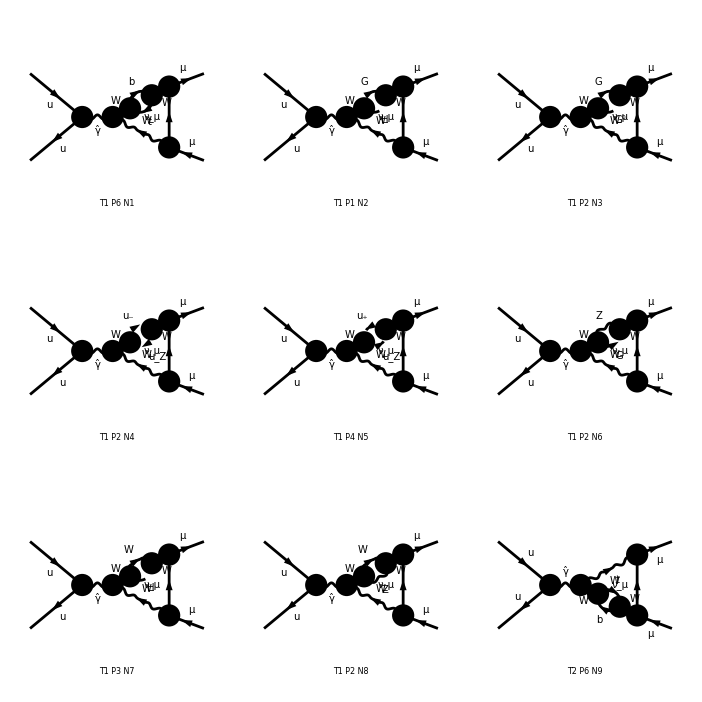

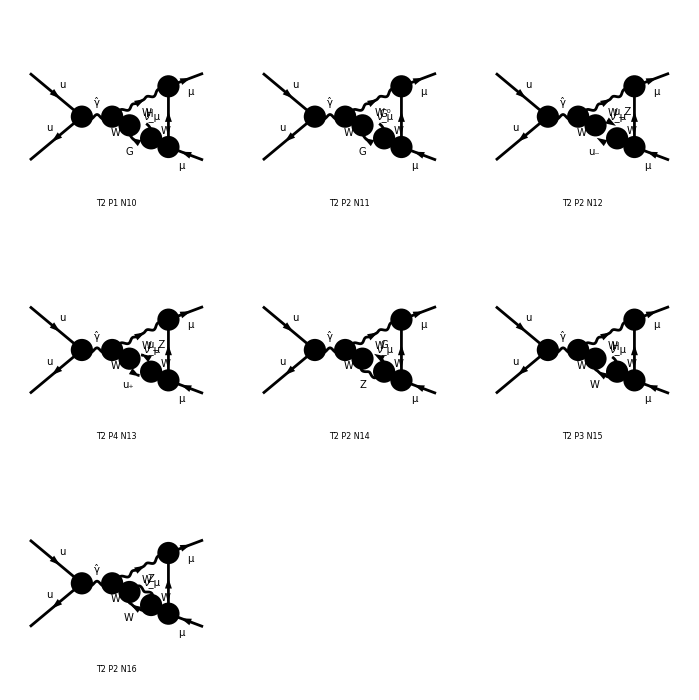

```mathematica
Paint[DiagramExtract[fields2Lnoplanar,indexPlByMass]];
```

```mathematica
ImportInput[]
Do[If[ShiftToIntegralFamily[plByMass[[i]]]==={},Print[i," ",plByMass[[i]]],Print[ShiftToIntegralFamily[plByMass[[i]]]]],{i,1,Length[plByMass]}]
```

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm2L_noplanar_massless_notr/ifdefinition/input/kinematics.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm2L_noplanar_massless_notr/ifdefinition/input/integral_families.m.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm2L_noplanar_massless_notr/ifdefinition/input/equivalence_classes.m

{{p1→p1,p2→p2,p3→p3,q1→q1,q2→p3+q1-q2}}

{{p1→p1,p2→p2,p3→p3,q1→q2,q2→p3-q1}}

{{p1→p1+p2-p3,p2→p3,p3→p2,q1→p1+q2,q2→p3+q1+q2}}

{{p1→p1+p2-p3,p2→p3,p3→p2,q1→p1+q2,q2→p3+q1+q2}}

{{p1→p1+p2-p3,p2→p3,p3→p2,q1→p1+q2,q2→p3+q1+q2}}

{{p1→p1+p2-p3,p2→p3,p3→p2,q1→p1+q2,q2→p1+p2-p3-q1}}

{{p1→p1,p2→p2,p3→p3,q1→q2,q2→p3-q1}}

{{p1→p1+p2-p3,p2→p3,p3→p2,q1→p1+q2,q2→p3+q1+q2}}

{{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→p3+q1-q2}}

{{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q2,q2→p3-q1}}

{{p1→p1+p2-p3,p2→p3,p3→p2,q1→p1+q2,q2→-p3-q1-q2}}

{{p1→p1+p2-p3,p2→p3,p3→p2,q1→p1+q2,q2→-p3-q1-q2}}

{{p1→p1+p2-p3,p2→p3,p3→p2,q1→p1+q2,q2→-p3-q1-q2}}

{{p1→p1+p2-p3,p2→p3,p3→p2,q1→p1+q2,q2→p3+q1}}

{{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q2,q2→p3-q1}}

{{p1→p1+p2-p3,p2→p3,p3→p2,q1→p1+q2,q2→-p3-q1-q2}}

```mathematica
k=1;
plByMass[[k]]
ShiftToIntegralFamily[plByMass[[k]]]
plByMass[[k]]/.ShiftToIntegralFamily[plByMass[[k]]]
ExtractFamily[plByMass[[k]]/.ShiftToIntegralFamily[plByMass[[k]]]]
```

PropList[KiraPropagator[q1,0],KiraPropagator[p3+q1,mw],KiraPropagator[-p1-p2+p3+q1,mw],KiraPropagator[q2,0],KiraPropagator[p1+p2-p3-q1+q2,mw]]

{{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q2,q2→-p3+q1}}

{PropList[KiraPropagator[-p3+q1,0],KiraPropagator[-p3-q2,mw],KiraPropagator[p1+p2-p3-q2,mw],KiraPropagator[-q2,0],KiraPropagator[q1+q2,mw]]}

{D8,{mw}}

```mathematica
ImportInput[]
```

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm2L_noplanar_massless_notr/ifdefinition/input/kinematics.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm2L_noplanar_massless_notr/ifdefinition/input/integral_families.m.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/maindir/pmm2L_noplanar_massless_notr/ifdefinition/input/equivalence_classes.m

```mathematica
k=1;
pl[[k]]
ShiftToIntegralFamily[pl[[k]]]
pl[[k]]/.ShiftToIntegralFamily[pl[[k]]]
ExtractFamily[pl[[k]]/.ShiftToIntegralFamily[pl[[k]]]]
```

{PropList[KiraPropagator[q1,0],KiraPropagator[-p3+q1,0],KiraPropagator[q2,0],KiraPropagator[-p1-p2+p3+q2,mw],KiraPropagator[q1+q2,mw]]}

{{p1→p2,p2→p1,p3→p1+p2-p3,q1→q2,q2→q1}}

{{PropList[KiraPropagator[q1,0],KiraPropagator[-p3+q1,mw],KiraPropagator[q2,0],KiraPropagator[-p1-p2+p3+q2,0],KiraPropagator[q1+q2,mw]]}}

{C4,{mw}}

```mathematica
Do[If[ShiftToIntegralFamily[pl[[i]]]=!={},Print[i," ",ShiftToIntegralFamily[pl[[i]]],"  ",ExtractFamily[pl[[i]]/.ShiftToIntegralFamily[pl[[i]]]]]],{i,1,Length[pl]}]
```

1 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→q2,q2→q1}}  {C4,{mw}}

2 {{p1→p1,p2→p2,p3→p3,q1→q1,q2→q2}}  {C4,{mw}}

3 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→q2,q2→q1}}  {D11,{mw,mz}}

4 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→q2,q2→q1}}  {C5,{mw,mz}}

5 {{p1→p1,p2→p2,p3→p3,q1→q1,q2→q2}}  {C5,{mw,mz}}

6 {{p1→p1,p2→p2,p3→p3,q1→q1,q2→q2}}  {D1,{0}}

7 {{p1→p1,p2→p2,p3→p3,q1→q1,q2→q2}}  {D2,{mz}}

$Aborted

```mathematica
Do[
ShiftAndSave[i,j];
,{i,1,278},{j,1}]
```

ABISS: Integral family {{B1, {0}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_101_1.m.

ABISS: Integral family {{B5, {mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_102_1.m.

ABISS: Integral family {{B6, {mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_103_1.m.

ABISS: Integral family {{B7, {mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_104_1.m.

ABISS: Integral family {{B7, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_105_1.m.

ABISS: Integral family {{B8, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_119_1.m.

ABISS: Integral family {{B8, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_120_1.m.

ABISS: Integral family {{B9, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_121_1.m.

ABISS: Integral family {{B10, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_122_1.m.

ABISS: Integral family {{B10, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_123_1.m.

ABISS: Integral family {{B9, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_124_1.m.

ABISS: Integral family {{B11, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_125_1.m.

ABISS: Integral family {{B11, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_126_1.m.

ABISS: Integral family {{B13, {mw, mh}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_127_1.m.

ABISS: Integral family {{B13, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_128_1.m.

ABISS: Integral family {{B8, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_149_1.m.

ABISS: Integral family {{B8, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_150_1.m.

ABISS: Integral family {{B8, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_151_1.m.

ABISS: Integral family {{B8, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_152_1.m.

ABISS: Integral family {{B9, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_153_1.m.

ABISS: Integral family {{B10, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_154_1.m.

ABISS: Integral family {{B10, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_155_1.m.

ABISS: Integral family {{B9, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_156_1.m.

ABISS: Integral family {{B9, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_157_1.m.

ABISS: Integral family {{B10, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_158_1.m.

ABISS: Integral family {{B10, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_159_1.m.

ABISS: Integral family {{B9, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_160_1.m.

ABISS: Integral family {{B11, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_161_1.m.

ABISS: Integral family {{B11, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_162_1.m.

ABISS: Integral family {{B11, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_163_1.m.

ABISS: Integral family {{B11, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_164_1.m.

ABISS: Integral family {{B12, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_165_1.m.

ABISS: Integral family {{B13, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_166_1.m.

ABISS: Integral family {{B12, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_167_1.m.

ABISS: Integral family {{B13, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_168_1.m.

ABISS: Integral family {{B2, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_169_1.m.

ABISS: Integral family {{B15, {mz, mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_170_1.m.

ABISS: Integral family {{B14, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_171_1.m.

ABISS: Integral family {{B8, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_194_1.m.

ABISS: Integral family {{B8, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_195_1.m.

ABISS: Integral family {{B9, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_196_1.m.

ABISS: Integral family {{B10, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_197_1.m.

ABISS: Integral family {{B10, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_198_1.m.

ABISS: Integral family {{B9, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_199_1.m.

ABISS: Integral family {{B11, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_200_1.m.

ABISS: Integral family {{B11, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_201_1.m.

ABISS: Integral family {{B12, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_202_1.m.

ABISS: Integral family {{B13, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_203_1.m.

ABISS: Integral family {{B8, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_204_1.m.

ABISS: Integral family {{B8, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_205_1.m.

ABISS: Integral family {{B9, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_206_1.m.

ABISS: Integral family {{B10, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_207_1.m.

ABISS: Integral family {{B10, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_208_1.m.

ABISS: Integral family {{B9, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_209_1.m.

ABISS: Integral family {{B11, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_210_1.m.

ABISS: Integral family {{B11, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_211_1.m.

ABISS: Integral family {{B13, {mw, mh}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_212_1.m.

ABISS: Integral family {{B8, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_225_1.m.

ABISS: Integral family {{B8, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_226_1.m.

ABISS: Integral family {{B9, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_227_1.m.

ABISS: Integral family {{B10, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_228_1.m.

ABISS: Integral family {{B10, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_229_1.m.

ABISS: Integral family {{B9, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_230_1.m.

ABISS: Integral family {{B11, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_231_1.m.

ABISS: Integral family {{B11, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_232_1.m.

ABISS: Integral family {{B12, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_233_1.m.

ABISS: Integral family {{B13, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_234_1.m.

ABISS: Integral family {{C1, {0}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_257_1.m.

ABISS: Integral family {{C2, {mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_258_1.m.

ABISS: Integral family {{C3, {mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_259_1.m.

ABISS: Integral family {{C4, {mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_260_1.m.

ABISS: Integral family {{C5, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_275_1.m.

ABISS: Integral family {{C6, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_276_1.m.

ABISS: Integral family {{C7, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_277_1.m.

ABISS: Integral family {{C8, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_278_1.m.

```mathematica
propMasses[prop_PropList]:=Module[{result},
result=List@@prop;
result=result/.KiraPropagator[_,m_]:>m;
Return[result]
]
```

```mathematica
numberOfMasses[prop_PropList]:=Length[DeleteCases[propMasses[prop],0]]
```

```mathematica
propMasses[pl[[9]]]
```

propMasses[1/s^2(-2 mm^2+s) (-2 mu^2+s) PropList[KiraPropagator[q1,mm],KiraPropagator[p3+q1,mz],KiraPropagator[-p1-p2+p3+q1,0],KiraPropagator[q2,mw],KiraPropagator[p1+p2+q2,mw],KiraPropagator[p3+q1+q2,mw]]]

```mathematica
numberOfMasses[pl[[9]]]
```

4

## Paint

> Top. 1 aebe/cfdg/ehfg1f1h212g2h.m, 0 diagrams

> Top. 2 aebe/cfdg/eh1f1g1h2f2g2h.m, 0 diagrams

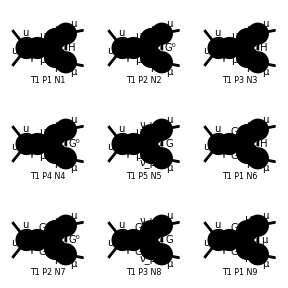

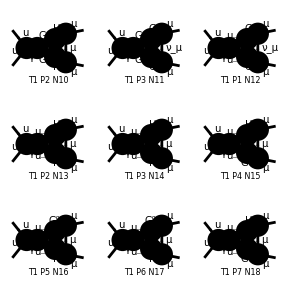

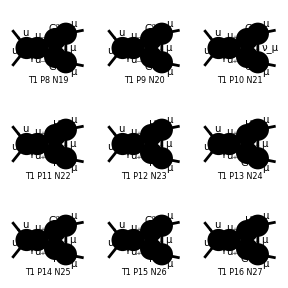

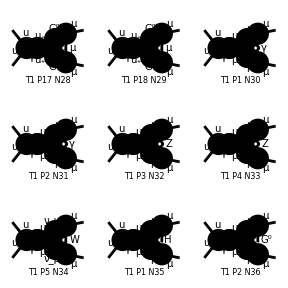

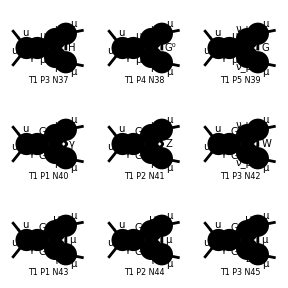

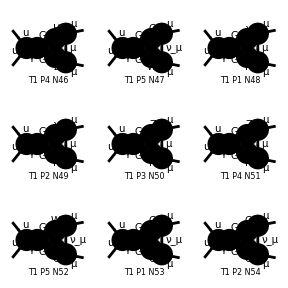

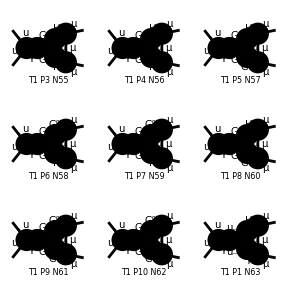

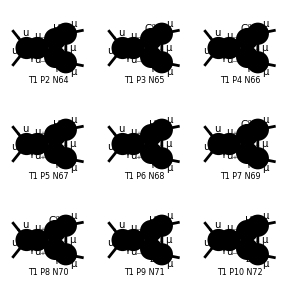

```mathematica
Paint[fields2LplanarnoT];
```

## Starting Input

## Lagrangian parameter replace

```mathematica
parameterReplace=<<(NotebookDirectory[]<>"smparameters.m");
chargeReplace={Ql->-1,I3l->-1/2,I3N->1/2,Qu->2/3,I3u->1/2,Qd->-1/3,I3d->-1/2};
cwReplace={cw->Sqrt[1-sw^2],mw->mz Sqrt[1-sw^2]};
complexReplace={mzC->mz,gZlLC->gZlL, gZlRC->gZlR, gZuLC->gZuL, gZuRC->gZuR};
```

Get::noopen: Cannot open \!\(\*RowBox[{"\"/home/riccardo/Documents/Fisica/Tesi/maindir/pmm2L_noplanar_massless_notr/ifdefinition/smparameters.m\""}]\).

## Functions

### Kira Propagator extraction

```mathematica
extractKiraProp[sm_]:=Module[{result,smtmp,kp,p},
smtmp=sm(*//Simplify*);
If[MatchQ[smtmp,PropList[p__]*expr_],
result=smtmp/.PropList[p__]*expr_->{p};
result=Times@@result;
];
If[!MatchQ[smtmp,PropList[p__]*expr_],
result=1;
];
Return[result]
];
```

```mathematica
extractMomenta[sm_]:=Module[{result,kpprod},
kpprod=extractKiraProp[sm];
If[kpprod===1, result={}];
If[Head[kpprod]===KiraPropagator, result=kpprod[[1]]];
If[Head[kpprod]===Times,
result=Map[#[[1]]&,List@@kpprod]
];
Return[result]
];
```

```mathematica
l=2;
ExtractFamily[sm[[l]]]
extractKiraProp[sm[[l]]]
```

{{False}}

KiraPropagator[q1,mm] KiraPropagator[p3+q1,mh] KiraPropagator[-p1-p2+p3+q1,mh] KiraPropagator[q2,mm] KiraPropagator[p1+p2+q2,mm] KiraPropagator[p3+q1+q2,mm]

### Analogous integral families

```mathematica
sameIntegral[ui1_userIntegral,ui2_userIntegral]:=Module[{if1,if2,test1,test2},
if1=ui1[[1]];
if2=ui2[[1]];
test1=userPropagatorMomenta[if1]^2-masses[ui1]^2;
test2=userPropagatorMomenta[if2]^2-masses[ui2]^2;
test1=test1^extractIndices[ui1];
test2=test2^extractIndices[ui2];
Return[test1===test2]
];
```

```mathematica
massIndex[mi_]:=ToExpression[StringDrop[ToString[mi],1]]
```

```mathematica
massSub[0,ui_userIntegral]:=0;
massSub[mi_,ui_userIntegral]:=ui[[2,massIndex[mi]]];
```

```mathematica
masses[ui_userIntegral]:=Module[{masses,massesReplace},
masses=Map[massSub[#,ui]&,userIntegralMasses[ui[[1]]]];
Return[masses]
];
```

```mathematica
extractIndices[ui_userIntegral]:=Delete[List@@ui,{{1},{2}}];
```

### Scalar integrals manipulation

```mathematica
si=<<(NotebookDirectory[]<>"scalar_integrals.m");
```

Get::noopen: Cannot open \!\(\*RowBox[{"\"/home/riccardo/Documents/Fisica/Tesi/maindir/pmm2L_noplanar_massless_notr/ifdefinition/scalar_integrals.m\""}]\).

```mathematica
mi=<<(NotebookDirectory[]<>"coefficients/Masters.m");
```

Get::noopen: Cannot open \!\(\*RowBox[{"\"/home/riccardo/Documents/Fisica/Tesi/maindir/pmm2L_noplanar_massless_notr/ifdefinition/coefficients/Masters.m\""}]\).

```mathematica
rules=<<(NotebookDirectory[]<>"kira_myintegrals.m");
```

Get::noopen: Cannot open \!\(\*RowBox[{"\"/home/riccardo/Documents/Fisica/Tesi/maindir/pmm2L_noplanar_massless_notr/ifdefinition/kira_myintegrals.m\""}]\).

```mathematica
substitution[si_userIntegral,rules_]:=Module[{result,rsi},
rsi=reduce[si];
result=rsi/.rules;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
substitute[si_userIntegral,rules_]:=Module[{result,m,mass,if,name,rsi},
m=si/.userIntegral[name_,mass_,x__]->mass;
if=si/.userIntegral[name_,mass_,x__]->name;
rsi=reduce[si];
result=rsi/.rules;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
masterReduction[si_userIntegral,rules_]:=Module[{result,m,mass,if,name,rsi,ifpattern,ifreplace},
m=si/.userIntegral[name_,mass_,x__]->mass;
if=si/.userIntegral[name_,mass_,x__]->name;
rsi=reduce[si];
result=rsi/.rules;
ifreplace=Map[#[x__]->userIntegral[#,DeleteCases[DeleteDuplicates[userIntegralMasses[#]],0],x]&,userIntegralFamiliesNames];
result=result/.ifreplace;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
reduce[si_userIntegral]:=Module[{result,name,x},
result=si/.userIntegral[name_,mass_,x__]->name[x];
Return[result]
]
```

```mathematica
massReplace[si_userIntegral]:=Module[{result,m,mass},
m=si/.userIntegral[name_,mass_,x__]->mass;
result=Array[(ToExpression[StringJoin["m",ToString[#]]]->m[[#]])&,Length[m]];
Return[result];
]
```

```mathematica
sectorList[si_List]:=Module[{result,l,x},
result=Array[0 &,9];
Do[
l=si[[i]]/.userIntegral[name_,mass_,x__]->{x};
Do[
If[l[[j]]>0,
result[[j]]=1
],
{j,Length[l]}]
,{i,Length[si]}];
Return[result]
]
```

```mathematica
si//sectorList
```

sectorList[$Failed]

```mathematica
si
```

$Failed

```mathematica
??Export
```

### Find r and s of UserIntegral lists

```mathematica
findR[si_List]:=Module[{rList,result},
rList=Map[sumPlus,si];
result=Max[rList];
Return[result]
];
```

```mathematica
findS[si_List]:=Module[{rList,result},
rList=Map[sumMinus,si];
result=Max[rList];
Return[result]
];
```

```mathematica
sumPlus[ui_userIntegral]:=Module[{indexList,result},
indexList=extractIndices[ui];
indexList=Map[positive,indexList];
result=Plus@@indexList;
Return[result]
];
```

```mathematica
sumMinus[ui_userIntegral]:=Module[{indexList,result},
indexList=-extractIndices[ui];
indexList=Map[positive,indexList];
result=Plus@@indexList;
Return[result]
];
```

```mathematica
positive[i_Integer]:=Module[{result},
If[i≥0,result=i];
If[i<0,result=0];
Return[result]
];
```

```mathematica
collectByIFname[si_List,name_]:=Module[{result},
result=DeleteDuplicates[Cases[si,userIntegral[name,___],Infinity]];
Return[result]
]
```

```mathematica
findActiveSectors[si_List]:=Module[{result,sectors,x},
result=ConstantArray[0,9];
Do[
sectors=si[[i]]/.userIntegral[_,_,x__]:>{x};
Do[
If[sectors[[j]]>0,result[[j]]=1]
,{j,Length[sectors]}]
,{i,Length[si]}];
Return[result]
]
```

### Scalar integrals manipulation

```mathematica
si=<<(NotebookDirectory[]<>"scalar_integrals.m");
```

Get::noopen: Cannot open \!\(\*RowBox[{"\"/home/riccardo/Documents/Fisica/Tesi/maindir/pmm2L_noplanar_massless_notr/ifdefinition/scalar_integrals.m\""}]\).

```mathematica
mi=<<(NotebookDirectory[]<>"coefficients/Masters.m");
```

Get::noopen: Cannot open \!\(\*RowBox[{"\"/home/riccardo/Documents/Fisica/Tesi/maindir/pmm2L_noplanar_massless_notr/ifdefinition/coefficients/Masters.m\""}]\).

```mathematica
rules=<<(NotebookDirectory[]<>"kira_myintegrals.m");
```

Get::noopen: Cannot open \!\(\*RowBox[{"\"/home/riccardo/Documents/Fisica/Tesi/maindir/pmm2L_noplanar_massless_notr/ifdefinition/kira_myintegrals.m\""}]\).

```mathematica
substitution[si_userIntegral,rules_]:=Module[{result,rsi},
rsi=reduce[si];
result=rsi/.rules;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
substitute[si_userIntegral,rules_]:=Module[{result,m,mass,if,name,rsi},
m=si/.userIntegral[name_,mass_,x__]->mass;
if=si/.userIntegral[name_,mass_,x__]->name;
rsi=reduce[si];
result=rsi/.rules;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
masterReduction[si_userIntegral,rules_]:=Module[{result,m,mass,if,name,rsi,ifpattern,ifreplace},
m=si/.userIntegral[name_,mass_,x__]->mass;
if=si/.userIntegral[name_,mass_,x__]->name;
rsi=reduce[si];
result=rsi/.rules;
ifreplace=Map[#[x__]->userIntegral[#,DeleteCases[DeleteDuplicates[userIntegralMasses[#]/.{M1->m1,M2->m2,M3->m3}],0],x]&,userIntegralFamiliesNames];
result=result/.ifreplace;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
reduce[si_userIntegral]:=Module[{result,name,x},
result=si/.userIntegral[name_,mass_,x__]->name[x];
Return[result]
]
```

```mathematica
massReplace[si_userIntegral]:=Module[{result,m,mass},
m=si/.userIntegral[name_,mass_,x__]->mass;
result=Array[(ToExpression[StringJoin["m",ToString[#]]]->m[[#]])&,Length[m]];
Return[result];
]
```

### Field Insertions manipulations

```mathematica
countInsertions[ins_]:=Module[{result,index},
result=0;
Do[
Do[
result+=Length[ins[[i,2,j,2]]];
,{j,Length[ins[[i,2]]]}];
,{i,Length[ins]}];
Return[result]
]
```

```mathematica
extractTopology[ins_Rule]:=ins[[1]];

extractLoopFields[top_]:=Module[{result},
result=Cases[top,Propagator[Loop[_]][Vertex[a1_][n1_],Vertex[a2_][n2_],f_]:>Rule[{n1,n2},f],Infinity]
]

extractLoopVertices[lines_]:=Module[{result},
result=Cases[lines,Rule[{n1_,n2_},f_]:>{n1,n2},Infinity]
]

next[{a_,b_},c_]:=Module[{result},
If[a=!=c && b=!=c,
result=c,
If[a===c,
result=b,
result=a
]
];
Return[result]
]

sortLoopFields[lines_List]:=Module[{result},
result=SortBy[lines,#[[2,1]]&]
]

triangles[top_]:=Module[{result,lines,vertices,a,b,c,verticesTmp,f1,f2,f3},
result={};
lines=extractLoopFields[top];
vertices=Map[Sort,extractLoopVertices[lines]];
Do[
a=vertices[[i,1]];
b=vertices[[i,2]];
verticesTmp=Delete[vertices,i];
Do[
If[!FreeQ[verticesTmp[[j]],a],
c=next[verticesTmp[[j]],a];
If[(!FreeQ[verticesTmp,Sort[{b,c}]]),
f1=Sort[{a,b}]/.lines;
f2=Sort[{a,c}]/.lines;
f3=Sort[{b,c}]/.lines;
result=AppendTo[result,sortLoopFields[{{Sort[{a,b}],f1},{Sort[{a,c}],f2},{Sort[{b,c}],f3}}]]
]
]
,{j,Length[verticesTmp]}]
,{i,Length[vertices]}];
Return[DeleteDuplicates[result]]
]

fermion[field_]:=Module[{result},
result=field;
If[MatchQ[field,-F[__]],
result=-field
];
Return[result]
]

deleteFermionTriangles[insertion_]:=Module[{result,n,diag,tri,rules,fields,check,deletelist},
n=countInsertions[insertion];
deletelist={};
Do[
diag=DiagramExtract[insertion,i];
tri=triangles[diag[[1,1]]];
rules=List@@diag[[1,2,1,2,1]];
If[tri=!={},
Do[
fields=Map[fermion[#[[2]]]&,tri[[j]]/.rules];
If[MatchQ[fields,{F[__],F[__],F[__]}]||MatchQ[fields,{-F[__],-F[__],-F[__]}],
deletelist=AppendTo[deletelist,i]
]
,{j,Length[tri]}]
]
,{i,n}];
deletelist=DeleteDuplicates[deletelist];
result=DiagramDelete[insertion,deletelist];
Return[result]
]
```

```mathematica
deleteFermionTriangles[fields2Lplanar]
```

TopologyList[Process→{F[3,{1,o}],-F[3,{1,o}]}→{F[2,{2}],-F[2,{2}]},Model→{SMbgf_Anglerfish},GenericModel→{Lorentzbgf},InsertionLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][5],Field[2]],7,Propagator[Loop[1]][Vertex[3][-2],Vertex[3][7],Field[10]],Propagator[Loop[1]][Vertex[3][-2],Vertex[3][8],Field[11]]]→Insertions[Generic][1],1]
 |  |  |  |

### Coefficient Manipulation

```mathematica
notNull[x_]:=Module[{result},
If[x===0,result=0,result=1];
Return[result]
]
contributions[coefflist_List]:=Module[{result},
If[MatrixQ[coefflist],
result=Map[notNull,coefflist,{2}];
Return[result]
,
Message[contributions::nomatrix,"Argument is not a matrix"];
Return[Null]
]
]
```

### Loop Checking

```mathematica
checkLoop[ins_,n_Integer]:=Module[{result},
result=!FreeQ[loopOrderList[ins],Centre[n]];
Return[result]
]
```

```mathematica
loopOrderList[ins_]:=Module[{result,n},
result=DeleteDuplicates[Cases[ToTree[ins[[1,1]]],Centre[n_][_]:>Centre[n],Infinity]];
Return[result]
]
```

### Contribution

```mathematica
contr[masters_List,coefficients_List]:=Module[{result},
If[Length[masters]===Length[coefficients],
result=Plus@@(masters*coefficients),
Message[contr::nomatrix,"Number of Masters different from number of coefficients"];
Return[Null]
];
Return[result]
]
```

### Sum of contributions

```mathematica
totContr[ndig_,nmas_,bornIndex_]:=Module[{result},
result=diagramCoefficients[[bornIndex,ndig,nmas]];
(*result=diagramCoefficientsRep[[ndig,1,nmas]]+diagramCoefficientsRep[[ndig,2,nmas]];*)
Return[result]
]
```

```mathematica
sumContr[nlist_List,nmas_,bornIndex_]:=Module[{result},
result=Simplify[Sum[totContr[nlist[[i]],nmas,bornIndex],{i,Length[nlist]}]];
Return[result]
]
```

```mathematica
totContrRep[ndig_,nmas_,bornIndex_]:=Module[{result},
result=diagramCoefficientsRep[[bornIndex,ndig,nmas]];
result=diagramCoefficientsRep[[ndig,1,nmas]]+diagramCoefficientsRep[[ndig,2,nmas]];
Return[result]
]
```

```mathematica
sumContrRep[nlist_List,nmas_,bornIndex_]:=Module[{result},
result=Simplify[Sum[totContrRep[bornIndex,nlist[[i]],nmas],{i,Length[nlist]}]];
Return[result]
]
```